```mathematica
(* Advanced adenoma data *) Gm={{57, 16.8,6.7,0.6},
{62,18.1,8.3,1.0},
{67,19.2,9.3,1.3},{72,19.9,10.1,2.0},{77,19.1,10.5,2.6},{58,17.9,7.1,0.7},{63,19.1,8.7,1.1},{68,20.1,9.7,1.5},{73,20.6,10.3,2.1},{78,19.6,10.6,2.7}}; 
Gf={{57,10.1,3.6,0.3},{62,11.4,4.6,0.5},{67,12.6,5.4,0.7},{72,13.7,6.2,1.1},{77,13.5,6.8,1.6},{58,10.9,3.9,0.4},{63,12.2,4.9,0.5},{68,13.4,5.6,0.8},{73,14.3,6.4,1.2},{78,13.9,7.0,1.7}};Kadv11=Table[{Gm[[i,1]], Sum[Gm[[i,k]],{k,3,4}]/100},{i,1,Length[Gm]}];Kadv21=Table[{Gf[[i,1]], Sum[Gf[[i,k]],{k,3,4}]/100},{i,1,Length[Gf]}];Kadv1=Sort[Kadv11]; Kadv2=Sort[Kadv21];Kadvave1=(Kadv1+Kadv2)/2;Kadvave=Sort[Kadvave1];
```

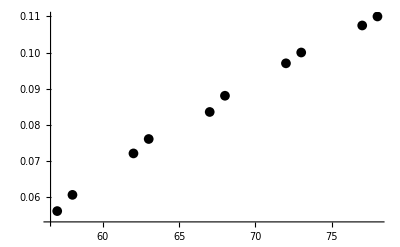

```mathematica
(* These are the incidence data we are fitting *) J0=ListPlot[{Kadvave},PlotMarkers->{Automatic,Offset[10]},PlotStyle->{Black,PointSize[Large]}]
```

```mathematica
K0=.; u=.; mu=.; p=.; Do[r0[i]=.;d0[i]=.;ga[i]=.,{i,1,6}]; Do[Do[rho[i,j]=.,{i,1,6}],{j,1,6}];Do[Do[R[i,j]=.; mut[i,j]=.;,{i,1,6}],{j,1,6}];Kmax1=.;Kmax2=.;delta=.;W1=(1-(n[3][t]+n[4][t]+n[5][t])/Kmax1);W2=(1-(n[3][t]+n[4][t]+n[5][t])/Kmax2)
```

Unset::norep: Assignment on r0 for r0[1] not found.

Unset::norep: Assignment on d0 for d0[1] not found.

Unset::norep: Assignment on ga for ga[1] not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

1-(n[3][t]+n[4][t]+n[5][t])/Kmax2

```mathematica
Ncrypts=.; Do[in[i]=n[i][0]==0,{i,2,6}]; in[1]=n[1][0]==Ncrypts;
```

```mathematica
eq[1]=D[n[1][t],t]==0-(R[1,2]+R[1,4])*n[1][t]; eq[2]=D[n[2][t],t]==R[1,2]*n[1][t]+0*ga[2]*n[2][t]-(R[2,5]+R[2,3])*n[2][t]; eq[3]=D[n[3][t],t]==R[2,3]*n[2][t]+ga[3]*n[3][t]*W1-delta*n[3][t]-R[3,6]*n[3][t]; eq[4]=D[n[4][t],t]==R[1,4]*n[1][t]+ga[4]*n[4][t]*W2-delta*n[4][t]-R[4,5]*n[4][t]; eq[5]=D[n[5][t],t]==R[2,5]*n[2][t]+R[4,5]*n[4][t]+ga[4]*n[5][t]*W2-delta*n[5][t]-R[5,6]*n[5][t]; eq[6]=D[n[6][t],t]==R[5,6]*n[5][t]+R[3,6]*n[3][t]+ga[6]*n[6][t];
```

```mathematica
(* These are the ODEs *) EEQ=Flatten[Table[{eq[i],in[i]},{i,1,5}]]
```

{n[1]'[t]==-(R[1,2]+R[1,4]) n[1][t],n[1][0]==Ncrypts,n[2]'[t]==R[1,2] n[1][t]-(R[2,3]+R[2,5]) n[2][t],n[2][0]==0,n[3]'[t]==R[2,3] n[2][t]-delta n[3][t]-R[3,6] n[3][t]+ga[3] n[3][t] (1-(n[3][t]+n[4][t]+n[5][t])/Kmax1),n[3][0]==0,n[4]'[t]==R[1,4] n[1][t]-delta n[4][t]-R[4,5] n[4][t]+ga[4] n[4][t] (1-(n[3][t]+n[4][t]+n[5][t])/Kmax2),n[4][0]==0,n[5]'[t]==R[2,5] n[2][t]+R[4,5] n[4][t]-delta n[5][t]-R[5,6] n[5][t]+ga[4] n[5][t] (1-(n[3][t]+n[4][t]+n[5][t])/Kmax2),n[5][0]==0}

```mathematica
Do[Do[R[i,j]=K0*r0[i]*mut[i,j]*rho[i,j],{i,1,6}],{j,1,6}];Do[Do[mut[i,j]=0,{i,1,6}],{j,1,6}];mut[1,2]=2*u; mut[2,3]=u+p; mut[1,4]=mu; mut[2,5]=mu; mut[3,6]=mu; mut[4,5]=2*u; mut[5,6]=u+p;Do[Do[rho[i,j]=(1-d0[j]*r0[i]/r0[j]/d0[i])/(1-(d0[j]*r0[i]/r0[j]/d0[i])^K0),{i,1,6}],{j,1,6}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
rbase=.;multAPC1=.; multAPC2=.; multRAS=.; ga3=.; ga4=.;sub=Flatten[{u->10.^(-7),p->0.,mu->10.^(-9),K0->7,Table[d0[i]->1.,{i,1,6}],r0[1]->rbase,r0[2]->multAPC1*rbase,r0[3]->multAPC2*rbase,r0[4]->multRAS*rbase,r0[5]->multRAS*multAPC1*rbase,r0[6]->multRAS*multAPC2*rbase,Ncrypts->10.^7}];subdiv={ga[2]->10.^(-3),ga[3]->ga3+10.^(-3),ga[4]->ga4+10.^(-3),ga[5]->ga4+10.^(-3),ga[6]->ga3+ga4+10.^(-3)};
```

```mathematica
paramsNoGa={delta->0.05,Kmax1->1000,Kmax2->1000,multAPC1->1.6,multAPC2->3.76,multRAS->3.54}
```

{delta→0.05,Kmax1→1000,Kmax2→1000,multAPC1→1.6,multAPC2→3.76,multRAS→3.54}

```mathematica
gamin=0; gamax=0.4; Nga=50; shga=(gamax-gamin)/Nga;
```

```mathematica
(* Fix Kmax1, Kmax2, and fit gamma *) Rmin=365/5; Rmax=300;Ni=30;sh=(Rmax-Rmin)/Ni; Do[Rbase=Rmin+i*sh;Do[Do[gg3=gamin+i1*shga; gg4=gamin+i2*shga;Ot=NDSolve[EEQ/.sub/.subdiv/.paramsNoGa/.{rbase->Rbase}/.{ga3->gg3,ga4->gg4}/.{Lasp->1,Laspx->1},Table[n[i][t],{i,1,5}],{t,0,80}]; n6=n[6][t]/.Ot[[1]];n5=n[5][t]/.Ot[[1]]; n4=n[4][t]/.Ot[[1]]; n3=n[3][t]/.Ot[[1]];n2=n[2][t]/.Ot[[1]]; n1=n[1][t]/.Ot[[1]]; OtvP=NDSolve[{D[P[t],t]==((R[5,6]*n5+R[3,6]*n3)/.sub/.subdiv/.paramsNoGa/.{rbase->Rbase}/.{ga3->gg3,ga4->gg4}/.{Lasp->1,Laspx->1})*(1-P[t]),P[0]==0},P[t],{t,0,80}];PPPadvX[i,i1,i2]=P[t]/.OtvP[[1]];PPPadv[i,i1,i2]=(1-0.05/1.01199)*PPPadvX[i,i1,i2]/.{t->t-4.79(* 11.97*)}; FullE[i,i1,i2]=Sum[((PPPadv[i,i1,i2]/.{t->Kadvave[[k,1]]})-Kadvave[[k,2]])^2,{k,1,Length[Kadvave]-2}],{i1,0,Nga}],{i2,0,Nga}];Print[i],{i,0,Ni}]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

```mathematica
Do[min=100; Do[ Do[If[FullE[ii,i1,i2]<min,{min=FullE[ii,i1,i2]; Res[ii]={i1,i2}}],{i1,0,Nga}],{i2,0,Nga}],{ii,0,Ni}]
```

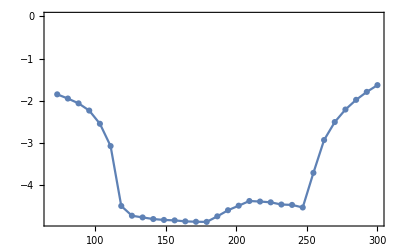

```mathematica
(* Figure 2(a) *)ListPlot[Table[{(Rmin+i*sh),Log[10,FullE[i,Res[i][[1]],Res[i][[2]]]]},{i,0,Ni}],PlotRange->All,PlotMarkers->Automatic,Joined->True,Frame->True, BaseStyle->Medium]
```

```mathematica
1.Table[{(Rmin+i*sh),Log[10,FullE[i,Res[i][[1]],Res[i][[2]]]]},{i,0,Ni}]
```

{{73.,-1.84946},{80.5667,-1.94901},{88.1333,-2.06338},{95.7,-2.23457},{103.267,-2.54815},{110.833,-3.07746},{118.4,-4.50004},{125.967,-4.73172},{133.533,-4.77207},{141.1,-4.81058},{148.667,-4.83191},{156.233,-4.8426},{163.8,-4.86576},{171.367,-4.8752},{178.933,-4.87833},{186.5,-4.74616},{194.067,-4.60137},{201.633,-4.49348},{209.2,-4.38232},{216.767,-4.39512},{224.333,-4.41356},{231.9,-4.46581},{239.467,-4.47506},{247.033,-4.53594},{254.6,-3.71371},{262.167,-2.93455},{269.733,-2.50737},{277.3,-2.21001},{284.867,-1.97999},{292.433,-1.79128},{300.,-1.63058}}

```mathematica
paramsNoK={delta->0.05,multAPC1->1.6,multAPC2->3.76,multRAS->3.54,ga3->0.2,ga4->0.07}
```

{delta→0.05,multAPC1→1.6,multAPC2→3.76,multRAS→3.54,ga3→0.2,ga4→0.07}

```mathematica
(* Fix gamma3, gamma4, and fit Kmax1, Kmax2  *) FM1=.;  Rmin=150; Rmax=270;Ni=20;sh=(Rmax-Rmin)/Ni;KKmin=1; KKmax=3.5; NK=150; shK=(KKmax-KKmin)/NK; Do[Rbase=Rmin+i*sh;Do[Do[KKsub1=10^(KKmin+i1*shK);KKsub2=10^(KKmin+i2*shK);Ot=NDSolve[EEQ/.sub/.subdiv/.paramsNoK/.{rbase->Rbase,Kmax1->KKsub1,Kmax2->KKsub2}/.{Lasp->1,Laspx->1},Table[n[i][t],{i,1,5}],{t,0,80}]; n6=n[6][t]/.Ot[[1]];n5=n[5][t]/.Ot[[1]]; n4=n[4][t]/.Ot[[1]]; n3=n[3][t]/.Ot[[1]];n2=n[2][t]/.Ot[[1]]; n1=n[1][t]/.Ot[[1]]; OtvP=NDSolve[{D[P[t],t]==((R[5,6]*n5+R[3,6]*n3)/.sub/.subdiv/.paramsNoK/.{rbase->Rbase,Kmax1->KKsub1,Kmax2->KKsub2}/.{Lasp->1,Laspx->1})*(1-P[t]),P[0]==0},P[t],{t,0,80}];PPPadvX[i,i1,i2]=P[t]/.OtvP[[1]];PPPadv[i,i1,i2]=(1-delta/1.01199)*PPPadvX[i,i1,i2]/.{t->t-4.79(*11.97*)}/.paramsNoK; (* Also calculate contributiion from different pathways *) OtvP1=NDSolve[{D[P[t],t]==((0*R[5,6]*n5+R[3,6]*n3)/.sub/.subdiv/.paramsNoK/.{rbase->Rbase,Kmax1->KKsub1,Kmax2->KKsub2}/.{Lasp->1,Laspx->1})*(1-P[t]),P[0]==0},P[t],{t,0,80}];
OtvP2=NDSolve[{D[P[t],t]==((R[5,6]*n5+0*R[3,6]*n3)/.sub/.subdiv/.paramsNoK/.{rbase->Rbase,Kmax1->KKsub1,Kmax2->KKsub2}/.{Lasp->1,Laspx->1})*(1-P[t]),P[0]==0},P[t],{t,0,80}];PPPadvX1[i,i1,i2]=P[t]/.OtvP1[[1]];PPPadvX2[i,i1,i2]=P[t]/.OtvP2[[1]];PPPadv1[i,i1,i2]=(1-delta/1.01199)*PPPadvX1[i,i1,i2]/.{t->t-4.79(*11.97*)}/.paramsNoK;PPPadv2[i,i1,i2]=(1-delta/1.01199)*PPPadvX2[i,i1,i2]/.{t->t-4.79(*11.97*)}/.paramsNoK;(* Now calculate the error *) FullE[i,i1,i2]=Sum[((PPPadv[i,i1,i2]/.{t->Kadvave[[k,1]]})-Kadvave[[k,2]])^2,{k,1,Length[Kadvave]-2}],{i1,0,NK}],{i2,0,NK}];Print[i],{i,0,Ni}]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

```mathematica
Do[min=100; Do[ Do[If[FullE[ii,i1,i2]<min,{min=FullE[ii,i1,i2]; Res1[ii]={i1,i2}}],{i1,0,NK}],{i2,0,NK}],{ii,0,Ni}]
```

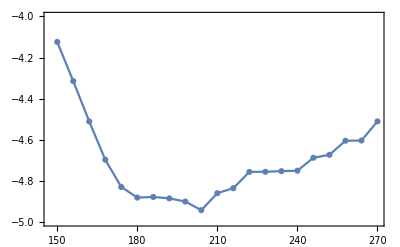

```mathematica
(* Figure 2(b) *)ListPlot[{Table[{Rmin+ii*sh,Log[10,FullE[ii,Res1[ii][[1]],Res1[ii][[2]]]]},{ii,0,20}]},Joined->True,Frame->True,PlotMarkers->Automatic,BaseStyle->Medium,PlotRange->{-5,-4}]
```

```mathematica
Table[{Rmin+ii*sh,Log[10,FullE[ii,Res1[ii][[1]],Res1[ii][[2]]]]},{ii,0,20}]
```

{{150,-4.12386},{156,-4.31454},{162,-4.5109},{168,-4.69706},{174,-4.82997},{180,-4.88161},{186,-4.87866},{192,-4.88542},{198,-4.9011},{204,-4.94292},{210,-4.86028},{216,-4.83583},{222,-4.75654},{228,-4.75599},{234,-4.75305},{240,-4.75083},{246,-4.68783},{252,-4.67345},{258,-4.605},{264,-4.60384},{270,-4.51067}}

InterpolatingFunction::dmval: Input value {-4.78837} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

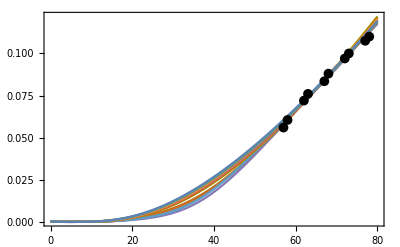

```mathematica
(* Figure 2(c) *) Show[Plot[Evaluate[Table[PPPadv[i,Res1[i][[1]],Res1[i][[2]]],{i,5,Ni}]],{t,0,80}],J0,Frame->True,BaseStyle->Medium]
```

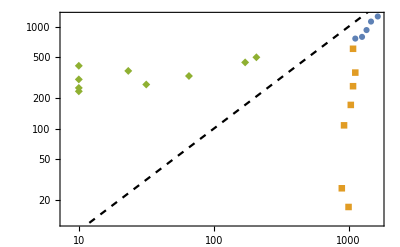

```mathematica
(* Figure 3(b) *) Show[ListLogLogPlot[{Table[{10^(KKmin+shK*Res1[ii][[1]]),10^(KKmin+shK*Res1[ii][[2]])},{ii,0,4}],Table[{10^(KKmin+shK*Res1[ii][[1]]),10^(KKmin+shK*Res1[ii][[2]])},{ii,5,11}],Table[{10^(KKmin+shK*Res1[ii][[1]]),10^(KKmin+shK*Res1[ii][[2]])},{ii,12,20}]},PlotMarkers->Automatic],LogLogPlot[x,{x,0,3000},PlotStyle->{Black,Dashed}],Frame->True,BaseStyle->Medium]
```

```mathematica
Table[{10^(KKmin+shK*Res1[ii][[1]]),10^(KKmin+shK*Res1[ii][[2]])},{ii,0,20}]
```

{{1646.9,1258.93},{1467.8,1122.02},{1359.36,926.119},{1258.93,794.328},{1122.02,764.422},{1079.78,607.202},{1122.02,354.813},{1079.78,261.016},{1039.12,171.133},{1000.,17.1133},{926.119,107.978},{891.251,26.1016},{207.332,501.187},{171.133,446.684},{10.,413.682},{23.2631,368.695},{65.5642,328.599},{10.,304.322},{31.6228,271.227},{10.,251.189},{10.,232.631}}

```mathematica
Export["/Users/komarova/Dropbox/AJAY/ASPIRIN/EPIDEMIOLOGY/RESUBMIT/Data3b.dat", Table[{10^(KKmin+shK*Res1[ii][[1]]),10^(KKmin+shK*Res1[ii][[2]])},{ii,0,20}]];
```

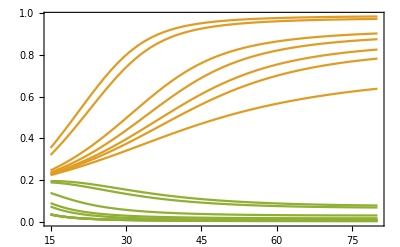

```mathematica
(* Figure 3(c) *) Plot[{I*Table[PPPadv1[ii,Res1[ii][[1]],Res1[ii][[2]]]/(PPPadv1[ii,Res1[ii][[1]],Res1[ii][[2]]]+PPPadv2[ii,Res1[ii][[1]],Res1[ii][[2]]]),{ii,0,4}],Table[PPPadv1[ii,Res1[ii][[1]],Res1[ii][[2]]]/(PPPadv1[ii,Res1[ii][[1]],Res1[ii][[2]]]+PPPadv2[ii,Res1[ii][[1]],Res1[ii][[2]]]),{ii,5,11}],Table[PPPadv1[ii,Res1[ii][[1]],Res1[ii][[2]]]/(PPPadv1[ii,Res1[ii][[1]],Res1[ii][[2]]]+PPPadv2[ii,Res1[ii][[1]],Res1[ii][[2]]]),{ii,12,20}]},{t,15,80},Frame->True,BaseStyle->Medium]
```